# Model Simulations, with forgetting

```mathematica
ClearAll["Global`*"];

(*set working directory that plots will go into*)
(*
SetDirectory["\\Users\\jabunce\\Dropbox\\Matsigenka-Mestizo_project_2014\\perception_analysis\\xcult_dynamics"];
*)
SetDirectory["/Users/johnbunce/Dropbox/Matsigenka-Mestizo_project_2014/perception_analysis/xcult_dynamics"];


(*Note that A and B in the following equations are the same as Groups S and L, respectively, in the text*)
```

## Functions

```mathematica
(*****************logistic function - increasing*************)
Logistic[x_]:=Module[{},1/(1+Exp[-1*x])];


(*****************Function to simulate phenotype evolution****************)
xcultsim[
matAinit_,(*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit_,(*(matrix) initial phenotype freqs in grp B: {{B11,B1X},{B2X,B22}}*)
tmax_,(*# sims*)
b_,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c_,(*cost of coordinating using norm that is not personally held*)
a_,(*(vector) probability of assorting to interact with members of your own group, rather than with outgroup {aA,aB}*)
m_,(*cost of having to learn and maintain cross-cultural competence*)
i_,(*identity valuation*)
muA_(*effect of a power difference on copying between groups*)
]:=Module[{},

(*intialize vectors and matrices*)
matA=matAinit;(*matrix of phenotypes in each group*)
matB=matBinit;
matAall=matAinit;(*list holding matrices of all phenotype freqs for group A over time*)
matBall=matBinit;
fitAtilde={{1,1},{1,1}};(*anticipated fitness of phenotypes in group A: {{A11,A1c},{A2c,A22}}*)
fitBtilde={{1,1},{1,1}};
fitAalltilde=fitAtilde;(*matrix holding all anticipated phenotype fitnesses for group A over time*)
fitBalltilde=fitBtilde;



(*simulation*)
For[t=1,t<=tmax,t++,


Clear[pA11,pA1X,pA2X,pA22,
pB11,pB1X,pB2X,pB22,
bA,bB,
wA11,wA1X,wA2X,wA22,
wB11,wB1X,wB2X,wB22,
wA11temp,wA1Xtemp,wA2Xtemp,wA22temp,
wB11temp,wB1Xtemp,wB2Xtemp,wB22temp,
wA11tildetemp,wA1Xtildetemp,wA2Xtildetemp,wA22tildetemp,
wB11tildetemp,wB1Xtildetemp,wB2Xtildetemp,wB22tildetemp,
poA1,poB1,
pAtildetot,pBtildetot];


(* Probability of observing attempts to use norm 1 by group A and norm 2 by group B indivs with in- and out-group *)

poA1in=pA11*(pA11+pA1X+pA2X+pA22)+
pA1X*(pA11+pA1X+1/2*pA2X)+
pA2X*(pA11+1/2*pA1X);

poA1out=pA11*(pB11+pB1X+pB2X+pB22)+
pA1X*(pB11+pB1X+1/2*pB2X)+
pA2X*(pB11+1/2*pB1X);


poB2in=pB22*(pB22+pB2X+pB1X+pB11)+
pB2X*(pB22+pB2X+1/2*pB1X)+
pB1X*(pB22+1/2*pB2X);

poB2out=pB22*(pA22+pA2X+pA1X+pA11)+
pB2X*(pA22+pA2X+1/2*pA1X)+
pB1X*(pA22+1/2*pA2X);



(*anticipated phenotype payoffs*)

wA11tildetemp=aA*poA1in+(1-aA)*(1-poB2out)*(1+bA)+i*poA1in*poB2out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA1Xtildetemp=aA*(poA1in+(1-poA1in)*(1-c))+
(1-aA)*((1-poB2out)*(1+bA)+poB2out*(1+bA-c))-m+i*poA1in*poB2out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA2Xtildetemp=aA*((1-poA1in)+poA1in*(1-c))+
(1-aA)*(poB2out*(1+bA)+(1-poB2out)*(1+bA-c))-m+i*(1-poA1in)*(1-poB2out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA22tildetemp=aA*(1-poA1in)+(1-aA)*poB2out*(1+bA)+i*(1-poA1in)*(1-poB2out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};



wB11tildetemp=aB*(1-poB2in)+(1-aB)*poA1out*(1+bB)+i*(1-poB2in)*(1-poA1out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB1Xtildetemp=aB*((1-poB2in)+poB2in*(1-c))+
(1-aB)*(poA1out*(1+bB)+(1-poA1out)*(1+bB-c))-m+i*(1-poB2in)*(1-poA1out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB2Xtildetemp=aB*(poB2in+(1-poB2in)*(1-c))+
(1-aB)*((1-poA1out)*(1+bB)+poA1out*(1+bB-c))-m+i*poB2in*poA1out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB22tildetemp=aB*poB2in+(1-aB)*(1-poA1out)*(1+bB)+i*poB2in*poA1out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};



(*anticipated total probability of all transitions from uni-cult competence*)

pA11tildetot=Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))]+
Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
Logistic[(muA*(wA2Xtilde-wA11tilde))]*
Logistic[(muA*(wA2Xtilde-wA1Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pA22tildetot=Logistic[(muA*(wA22tilde-wA1Xtilde))]*
Logistic[(muA*(wA22tilde-wA2Xtilde))]+
Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
Logistic[(muA*(wA2Xtilde-wA22tilde))]*
Logistic[(muA*(wA2Xtilde-wA1Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};



pB22tildetot=Logistic[(muA*(wB22tilde-wB2Xtilde))]*
Logistic[(muA*(wB22tilde-wB1Xtilde))]+
Logistic[(muA*(wB2Xtilde-wB22tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
Logistic[(muA*(wB1Xtilde-wB22tilde))]*
Logistic[(muA*(wB1Xtilde-wB2Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};


pB11tildetot=Logistic[(muA*(wB11tilde-wB2Xtilde))]*
Logistic[(muA*(wB11tilde-wB1Xtilde))]+
Logistic[(muA*(wB2Xtilde-wB11tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
Logistic[(muA*(wB1Xtilde-wB11tilde))]*
Logistic[(muA*(wB1Xtilde-wB2Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};



(*new phenotype frequencies after updating*)

pA11prime=aA*pA11*(pA11+
pA22*(Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))]+
Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA11tildetot)+
(1-aA)*pA11*(pB11+
pB22*(Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))]+
Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA11tildetot)+
aA*pA22*pA11*(Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA22tildetot+
(1-aA)*pA22*pB11*(Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA22tildetot//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pA22prime=1-pA11prime;
pA1Xprime=0;
pA2Xprime=0;




pB22prime=aB*pB22*(pB22+
pB11*(Logistic[(muA*(wB22tilde-wB2Xtilde))]*
Logistic[(muA*(wB22tilde-wB1Xtilde))]+
Logistic[(muA*(wB2Xtilde-wB22tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))])/pB22tildetot)+
(1-aB)*pB22*(pA22+
pA11*(Logistic[(muA*(wB22tilde-wB2Xtilde))]*
Logistic[(muA*(wB22tilde-wB1Xtilde))]+
Logistic[(muA*(wB2Xtilde-wB22tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))])/pB22tildetot)+
aB*pB11*pB22*(Logistic[(muA*(wB2Xtilde-wB11tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))])/pB11tildetot+
(1-aB)*pB11*pA22*(Logistic[(muA*(wB2Xtilde-wB11tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))])/pB11tildetot//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pB11prime=1-pB22prime;
pB1Xprime=0;
pB2Xprime=0;

(*update phenotype and fitness matrices*)
digs=300; (*number of decimal places to carry*)

matA = N[{{pA11prime,pA1Xprime},{pA2Xprime,pA22prime}},digs];
matB = N[{{pB11prime,pB1Xprime},{pB2Xprime,pB22prime}},digs];
fitAtilde=N[{{wA11tildetemp,wA1Xtildetemp},{wA2Xtildetemp,wA22tildetemp}},digs];
fitBtilde=N[{{wB11tildetemp,wB1Xtildetemp},{wB2Xtildetemp,wB22tildetemp}},digs];

(*accumulate phenotype freqs and fitnesses across sims*)
matAall=Join[matAall,matA];
matBall=Join[matBall,matB];
fitAalltilde=Join[fitAalltilde, fitAtilde];
fitBalltilde=Join[fitBalltilde, fitBtilde];

(*Print[Round[matAall, 0.01]]*)
];(*for t*)

];(*xcultsim*)
```

## Simulation Trajectories

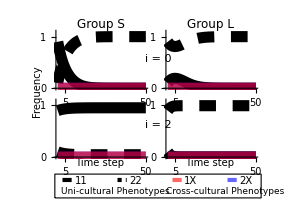

./figures/FigureTrajD_forget.pdf

```mathematica
(*matching pheno freqs: all machis and mestizos, just cross and uni-cult competence*)

(*A************ high in-group affinity *********************************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=1 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


figaA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,"5"},{50,"50"}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figaB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{White,9}},
Ticks->{{{5,"5"},{50,"50"}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];



(*B******************** increase i ******************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=2,(*identity valuation*)
muA=1 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figbA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{50,"50"},{5,"5"}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figbB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{White,9}},
Ticks->{{{5,"5"},{50,"50"}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];

(******************** assemble plots into Figure ****************************)
FigureTrajD=Panel[
GraphicsGrid[
{{figaA,figaB},{figbA,figbB}},

Spacings->{
{
Scaled[0.4], (*horizontal spacing: before, middle, end of row of figures*)
Scaled[0],
Scaled[0.2]
},
{
Scaled[0.3], (*vertical spacing: above, middles, bottom of column of figures*)
Scaled[0],
Scaled[1.5]
}
},

Frame->True,
FrameStyle->Directive[White],

Prolog->{
(*{AbsoluteThickness[3],GrayLevel[0.7],Opacity[1],Line[{{111,-8},{111,-470}}]},
{AbsoluteThickness[3],GrayLevel[0.7],Opacity[1],Line[{{472,-8},{472,-470}}]},*)

(*{AbsoluteThickness[1],Green,Opacity[1],Line[{{108,-8},{108,-470}}]},
{AbsoluteThickness[1],Green,Opacity[1],Line[{{475,-8},{475,-470}}]}*)
},

Epilog->{
Inset[Style["Group S",12],{240,-15}],
Inset[Style["Group L",12],{600,-15}],
Inset[Rotate[Style["Frequency",10],90Degree],{30,-231}],
(*Inset[Rotate[Style["Frequency",10],90Degree],{20,-342}],*)
Inset[Style["Time step",10],{235,-462}],
Inset[Style["Time step",10],{595,-462}],

(*Inset[Row[{Subscript[Style["a",Italic,8],Style["S",Italic,6]],Style[" = 4/5",8]}],{365,-85},{Left,Center}],*)
Inset[Row[{Style["i",Italic,8],Style[" = 0",8]}],{385,-125},{Left,Center}],

(*Inset[Row[{Subscript[Style["a",Italic,8],Style["S",Italic,6]],Style[" = 2/5",8]}],{365,-295},{Left,Center}],*)
Inset[Row[{Style["i",Italic,8],Style[" = 2",8]}],{385,-340},{Left,Center}],

x1=-85;
y1=-420;

{EdgeForm[Thin],White,(*Opacity[0.6],*)Rectangle[{175+x1,-78+y1},{850+x1,-155+y1}]},
Inset[Style["11",10],{260+x1,-100+y1}],
Inset[Style["Uni-cultural Phenotypes",9],{195+x1,-135+y1},{Left,Center}],
Inset[Style["22",10],{440+x1,-100+y1}],
Inset[Style["1X",10],{620+x1,-100+y1}],
Inset[Style["Cross-cultural Phenotypes",9],{540+x1,-135+y1},{Left,Center}],
Inset[Style["2X",10],{800+x1,-100+y1}],
{AbsoluteThickness[3],Black,Opacity[1],Line[{{200+x1,-97+y1},{230+x1,-97+y1}}]},
{AbsoluteThickness[3],CapForm["Butt"],Dashing[0.01],Black,Opacity[1],Line[{{380+x1,-97+y1},{410+x1,-97+y1}}]},
{AbsoluteThickness[3],Red,Opacity[0.6],Line[{{560+x1,-97+y1},{590+x1,-97+y1}}]},
{AbsoluteThickness[3],Blue,Opacity[0.6],Line[{{740+x1,-97+y1},{770+x1,-97+y1}}]}
},
ImageSize->300
],(*Graphics Grid*)
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,5}}
](*panel*)

Export["./figures/FigureTrajD_forget.pdf",FigureTrajD,"PDF"]
```